## Elasticity

```mathematica
Inv1[tensor_]:=Tr[tensor];
Inv2[tensor_]:=((Tr[tensor])^2-Tr[tensor.Transpose[tensor]])/2;
Inv3[tensor_]:=Det[tensor];

StrainGreen[mode_]:=Module[{SGr},
SGr=(Transpose[Deform]+Deform)/2;
If[mode=="nonlinear2"||mode=="nonlinear3",
SGr=SGr+(Transpose[Deform].Deform)/2];
SGrTemplate={
{Subscript[SG, xx],Subscript[SG, xy],Subscript[SG, xz]},
{Subscript[SG, yx],Subscript[SG, yy],Subscript[SG, yz]},
{Subscript[SG, zx],Subscript[SG, zy],Subscript[SG, zz]}};
SGrSubst={ 
Subscript[SG, xx]->SGr⟦1,1⟧,Subscript[SG, xy]->SGr⟦1,2⟧,Subscript[SG, xz]->SGr⟦1,3⟧,
Subscript[SG, yx]->SGr⟦2,1⟧,Subscript[SG, yy]->SGr⟦2,2⟧,Subscript[SG, yz]->SGr⟦2,3⟧,
Subscript[SG, zx]->SGr⟦3,1⟧,Subscript[SG, zy]->SGr⟦3,2⟧,Subscript[SG, zz]->SGr⟦3,3⟧};
I1 = Inv1[SGrTemplate];
I2 = Inv2[SGrTemplate];
I3 = Inv3[SGrTemplate];
E1 = Inv1[SGrTemplate];
E2 = Inv1[SGrTemplate.SGrTemplate];
E3 = Inv1[SGrTemplate.SGrTemplate.SGrTemplate];
SGr];

PotEnergyTempl[mode_,modules_]:=Module[{Pot},
Pot=(λ+2 μ)/2 I1^2-2 μ I2;
If[modules=="murnaghan",
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=Pot+(l+2 m)/3 I1^3-2 m I1 I2+n I3;
If[mode=="nonlinear3",
Pot=Pot+g1 I1^4+g2 I2^2+g3 I1 I3+g4 I2^2];],
If[modules=="landau",
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=Pot+CL/3 E1^3+BL E1 E2+AL/3 E3;
If[mode=="nonlinear3",
Pot=Pot+HL E1^4+GL E2^2+FL E1^2 E2+EL E1 E3];
],Throw["Unknown modules"]];
];
Pot];

PotEnergy[mode_,modules_]:=Module[{},
PotEnergyTempl[mode,modules]/.SGrSubst];

Piola[mode_,modules_]:=Module[{P,Pot},
If[mode=="linear",P=λ Inv1[SGr]IdentityMatrix[3]+2μ SGr//Simplify];
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=PotEnergyTempl[mode,modules];
P=(IdentityMatrix[3]+Deform).{
{D[Pot, Subscript[SG, xx]],D[Pot, Subscript[SG, xy]],D[Pot, Subscript[SG, xz]]},
{D[Pot, Subscript[SG, yx]],D[Pot, Subscript[SG, yy]],D[Pot, Subscript[SG, yz]]},
{D[Pot, Subscript[SG, zx]],D[Pot, Subscript[SG, zy]],D[Pot, Subscript[SG, zz]]}}/.SGrSubst ];
P];
```

## Uniaxial tension

```mathematica
ClearAll[U,V,W,λ,μ];
U=1+d;
Deform=1/2 DiagonalMatrix[{U^2-1,1/U-1,1/U-1}];
```

```mathematica
(* PMMA *)
AL=-1.41*10^9 a;
BL=-7.02*10^9 a;
CL=-3.91*10^9 a;
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/2/(1+ν);
Ε=4.92*10^9;
ν=0.34;
```

```mathematica
mode="nonlinear3";
modules="landau";
SGr=StrainGreen[mode];
Pot=PotEnergy[mode,modules];
P=Piola[mode,modules];
```

```mathematica
Stress[d_,a_,EL_,FL_,GL_,HL_]=P[[1,1]]//Simplify;
Stress[d_,a_]=Stress[d,a,0,0,0,0];
```

### Extension

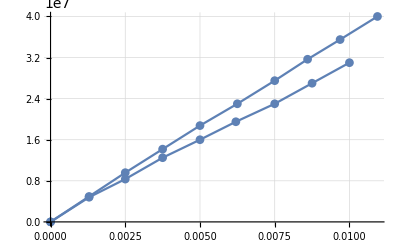

```mathematica
(* Data from Okeke 2017: quasi-static tension *)
ExperDataStaticExt={{0,0},{0.005,16.6*10^6},{0.01,29*10^6},{0.015,40*10^6},
{0.02,48*10^6},{0.025,54*10^6},{0.03,57*10^6}};
ExperDataStaticExtInterp=Interpolation[ExperDataStaticExt];

(* Data from Wu 2004: intermediate rate of tension 2.81 *)
ExperDataMedDynExt={{0,0},{0.00129,4.95*10^6},{0.0025,(10-5/12)*10^6},
{0.00375,(15-5/6)*10^6},{0.005,18.75*10^6},{0.00625,23*10^6},
{0.0075,27.5*10^6},{0.0086,(30+5/3)*10^6},{0.01-0.0025/8,35.5*10^6},
{0.01+0.0075/8,40*10^6}};
ExperDataMedDynExtInterp=Interpolation[ExperDataMedDynExt];
ExperDataMedDynExtSmooth[x_]=Fit[ExperDataMedDynExt,{x,x^2},x];

(* Data from Wu 2004: intermediate rate of tension 0.292 *)
ExperDataMedDynExt2={{0,0},{0.00129,4.8*10^6},{0.0025,(10-5/3)*10^6},
{0.00375,12.5*10^6},{0.005,16*10^6},{0.0062,19.5*10^6},{0.0075,23*10^6},
{0.00875,27*10^6},{0.01,31*10^6}};
ExperDataMedDynExtInterp2=Interpolation[ExperDataMedDynExt2];
ExperDataMedDynExtSmooth2[x_]=Fit[ExperDataMedDynExt2,{x,x^2},x];

Show[ListLinePlot[ExperDataMedDynExt,PlotMarkers->Automatic,GridLines->Automatic],
ListLinePlot[ExperDataMedDynExt2,PlotMarkers->Automatic,GridLines->Automatic]]
```

```mathematica
h=0.001;
(ExperDataStaticExtInterp[h]-ExperDataStaticExtInterp[0])/h
(ExperDataMedDynExtInterp[h]-ExperDataMedDynExtInterp[0])/h
```

3.7904×10^9

3.69506×10^9

#### 3rd order

3.67578×10^9 x

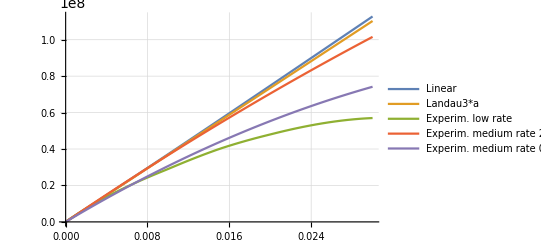

```mathematica
dmax=0.03;
f[x_]=Fit[Table[{d/1000,Stress[d/1000,1]},{d,0,0.001*1000}],{x},x]
Plot[{Stress[d,1],f[d],ExperDataStaticExtInterp[d],ExperDataMedDynExtSmooth[d],
ExperDataMedDynExtSmooth2[d]},{d,0,dmax},PlotRange-> All,GridLines->Automatic,
PlotLegends->{"Linear","Landau3*a","Experim. low rate","Experim. medium rate 2.81","Experim. medium rate 0.292"}]
```

```mathematica
dmax=0.03;
Manipulate[Plot[{f[d],Stress[d,a],ExperDataStaticExtInterp[d],ExperDataMedDynExtSmooth[d],ExperDataMedDynExtSmooth2[d]},{d,0,dmax},GridLines->Automatic,PlotLegends->{"Linear","Landau3*a","Experim. low rate","Experim. medium rate 2.81","Experim. medium rate 0.292"}],{a,1,10,0.5}]
```

#### 4th order

```mathematica
dmax=0.03;
data=Table[{d/1000,ExperDataMedDynExtSmooth2[d/1000]},{d,0,dmax*1000}];
```

```mathematica
fit=FindFit[data,Stress[d,a,EL,FL,GL,HL],{a,EL,FL,GL,HL},d]
```

{a→13.63,EL→-5.73709×10^15,FL→7.983×10^15,GL→7.19829×10^14,HL→-8.68654×10^15}

```mathematica
fit=FindFit[data,Stress[d,4,EL,FL,GL,HL],{EL,FL,GL,HL},d]
```

{EL→8.13349×10^15,FL→-1.13662×10^16,GL→-1.01829×10^15,HL→1.42276×10^16}

```mathematica
cons=10^12;
fit=FindFit[data,{Stress[d,4,EL,FL,GL,HL],Abs[EL]<cons,Abs[FL]<cons,Abs[GL]<cons,Abs[HL]<cons},{EL,FL,GL,HL},d]
```

{EL→1.×10^12,FL→1.×10^12,GL→-2.25849×10^11,HL→1.×10^12}

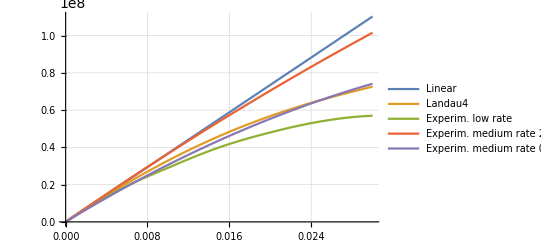

```mathematica
dmax=0.03;
Plot[{f[d],Stress[d,4,EL,FL,GL,HL]/.fit,ExperDataStaticExtInterp[d],ExperDataMedDynExtSmooth[d],ExperDataMedDynExtSmooth2[d]},{d,0,dmax},GridLines->Automatic,PlotLegends->{"Linear","Landau4","Experim. low rate","Experim. medium rate 2.81","Experim. medium rate 0.292"}]
```

```mathematica
sbst4order={EL->8.133486894830394*^15 b,FL->-1.1366203039813472*^16b,GL->-1.0182884423600852*^15b,HL->1.4227609644541294*^16b};
sbst4order={EL->1.*^12b,FL->1.*^12b,GL->-2.2584896459158383*^11b,HL->1.*^12b};
Stress[d_,a_,b_]=Stress[d,a,EL,FL,GL,HL]/.sbst4order;
```

```mathematica
dmax=0.03;
Manipulate[Plot[{Stress[d,a,b]/.sbst4order,ExperDataStaticExtInterp[d],ExperDataMedDynExtSmooth[d],ExperDataMedDynExtSmooth2[d]},{d,0,dmax},GridLines->Automatic,PlotLegends->{"Landau4","Experim. low rate","Experim. medium rate 2.81","Experim. medium rate 0.292"}],{a,1,10,0.5},{b,0,2,0.05}]
```

### Compression [needs correction]

```mathematica
(* Data from Zhang 2016: intermediate compression rate (0.1 s^-1) *)
ExperDataSlowDynComp={{-0.03,-20*10^6},{-0.025,-15.2*10^6},{-0.02,-10.8*10^6},
{-0.015,-7.2*10^6},{-0.01,-4*10^6},{-0.005,-1.6*10^6},{0,0}};
```

```mathematica
(* Data from Li 2001: rapid compression (1500 s^-1) *)
ExperDataFastDynComp={{0,0},{0.002,25*10^6},{0.04,50*10^6},
{0.01,74*10^6},{0.015,80*10^6},{0.02,125*10^6}};
ExperDataFastDynCompInterp=Interpolation[ExperDataFastDynComp];
```

```mathematica
dmax=0.02;
```

```mathematica
Stress[a_,d_]=Stress[d];
```

```mathematica
Manipulate[Plot[{-Stress[a,-d]//Simplify,ExperDataFastDynCompInterp[d]},{d,0,dmax},PlotRange->{0,2*10^8},GridLines->Automatic],{a,0,100,0.1}]
```

#### 4th order

```mathematica
mode="nonlinear3";
modules="landau";
SGr=StrainGreen[mode];
Pot=PotEnergy[mode,modules];
P=Piola[mode,modules];
```

```mathematica
AL=a AL0;BL=a BL0;CL=a CL0;
Stress2[d_]=P[[1,1]];
```

```mathematica
fit=FindFit[ExperDataFastDynComp,Stress2[d],{a,EL,FL,GL,HL},d]
```

{a→-571.139,EL→7.29173×10^17,FL→-1.01665×10^18,GL→-9.13867×10^16,HL→1.14011×10^18}

```mathematica
fit2=FindFit[ExperDataFastDynComp,Stress2[d]/.a->10,{EL,FL,GL,HL},d,Gradient->{D[ExperDataFastDynCompInterp[d],d]}]
```

{EL→-3.35219×10^17,FL→4.69365×10^17,GL→4.19485×10^16,HL→-6.14245×10^17}

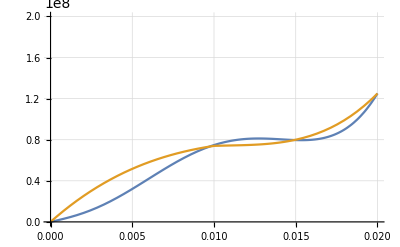

```mathematica
Plot[{(Stress2[d]/.fit2/.a->10),ExperDataFastDynCompInterp[d]},{d,0,dmax},PlotRange->{0,2*10^8},GridLines->Automatic]
```

```mathematica
EL=-b 3.3521917180042726*^17;FL=b 4.693649596145145*^17;
GL=b 4.194849811670641*^16;HL=-b 6.142447703972079*^17;
```

```mathematica
Stress2[a_,b_,d_]=Stress2[d];
```

```mathematica
Manipulate[Plot[{Stress2[a,b,d],ExperDataFastDynCompInterp[d]},{d,0,dmax},PlotRange->{0,2*10^8},GridLines->Automatic],{a,-10,10,0.1},{b,-1,1}]
```